```mathematica
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
```

TestReportObject[…]

### Basic Examples

View the code underlying a formatted expression:

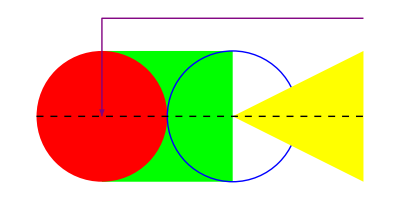
```mathematica
-Graphics-//ReadableForm
```

Graphics @ {
    RGBColor[ 0, 1, 0 ],
    Thickness @ Large,
    Rectangle[ { 0, -1 }, { 2, 1 } ],
    { RGBColor[ 1, 0, 0 ], Disk @ { 0, 0 } },
    { RGBColor[ 0, 0, 1 ], Circle @ { 2, 0 } },
    { RGBColor[ 1, 1, 0 ], Polygon @ { { 2, 0 }, { 4, 1 }, { 4, -1 } } },
    {
        RGBColor[ 0.5, 0, 0.5 ],
        Arrowheads @ Large,
        Arrow @ { { 4, 3 / 2 }, { 0, 3 / 2 }, { 0, 0 } },
        { GrayLevel[ 0 ], Dashing @ { Small, Small }, Line @ { { -1, 0 }, { 4, 0 } } }
    }
}

Visually inspect properties of formatted objects:

```mathematica
ResourceObject[…]//ReadableForm
```

ResourceObject[
    <|
        "Name" -> "LeNet Trained on MNIST Data",
        "UUID" -> "050b1a0a-f43a-4c28-b7e0-72607a918467",
        "ResourceType" -> "NeuralNet",
        "Version" -> "1.16.0",
        "Description" -> "Identify the handwritten digit in an image",
        "RepositoryLocation" ->
            URL[ "https://www.wolframcloud.com/objects/resourcesystem/api/1.0" ],
        "WolframLanguageVersionRequired" -> "11.1",
        "ContentElements" -> {
            "ConstructionNotebook",
            "ConstructionNotebookExpression",
            "EvaluationNet",
            "UninitializedEvaluationNet",
            "EvaluationExample"
        }
    |>,
    ResourceSystemBase -> "https://www.wolframcloud.com/objects/resourcesystem/api/1.0"
]

### Scope

Input-style syntax highlighting is used:

```mathematica
ReadableForm[Hold[f[x_]:=Table[i+1,{i,x}]]]
```

Hold[ f[ x_ ] := Table[ i + 1, { i, x } ] ]

Use Unevaluated to prevent the expression from evaluating:

```mathematica
ReadableForm[Unevaluated[Echo[∫_0^1 Log[1/2 (1+√(1+4 x))]/x ⅆx]]]
```

Echo @ Integrate[ Log[ (1 / 2) * (1 + Sqrt[ 1 + 4 * x ]) ] / x, { x, 0, 1 } ]

### Generalizations and Extensions

ToString will preserve the whitespace:

```mathematica
if=ReadableForm[TestResultObject[…]]
```

TestResultObject @ <|
    "TestClass" -> None,
    "TestIndex" -> 1,
    "TestID" -> None,
    "Outcome" -> "MessagesFailure",
    "Input" -> HoldForm[ 1 / 0 ],
    "ExpectedOutput" -> HoldForm @ DirectedInfinity[ ],
    "ActualOutput" -> HoldForm @ DirectedInfinity[ ],
    "ExpectedMessages" -> { },
    "ActualMessages" -> { HoldForm @ Message[ Power::infy, HoldForm[ 0^(-1) ] ] },
    "AbsoluteTimeUsed" -> Quantity[ 0., "Seconds" ],
    "CPUTimeUsed" -> Quantity[ 0., "Seconds" ],
    "MemoryUsed" -> Quantity[ 1136, "Bytes" ]
|>

```mathematica
ToString[if]
```

TestResultObject @ <|
    "TestClass" -> None,
    "TestIndex" -> 1,
    "TestID" -> None,
    "Outcome" -> "MessagesFailure",
    "Input" -> HoldForm[ 1 / 0 ],
    "ExpectedOutput" -> HoldForm @ DirectedInfinity[ ],
    "ActualOutput" -> HoldForm @ DirectedInfinity[ ],
    "ExpectedMessages" -> { },
    "ActualMessages" -> { HoldForm @ Message[ Power::infy, HoldForm[ 0^(-1) ] ] },
    "AbsoluteTimeUsed" -> Quantity[ 0., "Seconds" ],
    "CPUTimeUsed" -> Quantity[ 0., "Seconds" ],
    "MemoryUsed" -> Quantity[ 1136, "Bytes" ]
|>

CopyToClipboard will also preserve much of the formatting:

```mathematica
CopyToClipboard[if];
Paste[]
```

```mathematica
TestResultObject @ <|
    "TestClass" -> None,
    "TestIndex" -> 1,
    "TestID" -> None,
    "Outcome" -> "MessagesFailure",
    "Input" -> HoldForm[ 1 / 0 ],
    "ExpectedOutput" -> HoldForm @ DirectedInfinity[ ],
    "ActualOutput" -> HoldForm @ DirectedInfinity[ ],
    "ExpectedMessages" -> { },
    "ActualMessages" -> { HoldForm @ Message[ Power::infy, HoldForm[ 0^(-1) ] ] },
    "AbsoluteTimeUsed" -> Quantity[ 0., "Seconds" ],
    "CPUTimeUsed" -> Quantity[ 0., "Seconds" ],
    "MemoryUsed" -> Quantity[ 1136, "Bytes" ]
|>
```

### Options

#### CachePersistence

With CachePersistence→None, ReadableForm will not use any caching, which reduces overall memory usage but is the slowest method:

```mathematica
First[RepeatedTiming[ToString[ReadableForm[,CachePersistence->None]]]]
```

0.0192805

With the default behavior of CachePersistence→Automatic, ReadableForm will remember some values between evaluations to gain a modest performance boost:

```mathematica
First[RepeatedTiming[ToString[ReadableForm[,CachePersistence->Automatic]]]]
```

0.0112235

Using CachePersistence→Full will give the fastest performance, but the extra memory used is not released for the remainder of the kernel session:

```mathematica
First[RepeatedTiming[ToString[ReadableForm[,CachePersistence->Full]]]]
```

0.000142261

#### DynamicAlignment

ReadableForm can adjust indentation of certain parts of code in order to obtain alignment across lines when using a monospace font. Here is a helper function to display monospaced results:

```mathematica
showMonospace[expr_]:=Style[ToString[expr],PrivateFontOptions->{"OperatorSubstitution"->False},FontFamily->"Source Code Pro"];
```

```mathematica
showMonospace[expr=]
```

Hold[myFunction[] := Module[{result, anotherResult, test}, result = If[thisThing[], thenDoThatThing[], If[thisThing[], thenDoThatThing[], otherwiseDoSomethingElse[]]]; anotherResult = If[thisThing[], thenDoThatThing[], result = If[thisThing[], thenDoThatThing[], otherwiseDoSomethingElse[]]]; otherFunction[result, anotherResult, test]]]

By default, ReadableForm will only indent one step at a time:

```mathematica
ReadableForm[expr]//showMonospace
```

Hold[
    myFunction[ ] := 
        Module[ { result, anotherResult, test },
            
            result = 
                If[ thisThing[ ],
                    thenDoThatThing[ ],
                    If[ thisThing[ ],
                        thenDoThatThing[ ],
                        otherwiseDoSomethingElse[ ]
                    ]
                ];

            
            anotherResult = 
                If[ thisThing[ ],
                    thenDoThatThing[ ],
                    result = 
                        If[ thisThing[ ],
                            thenDoThatThing[ ],
                            otherwiseDoSomethingElse[ ]
                        ]
                ];

            otherFunction[ result, anotherResult, test ]
        ]
]

Use the setting "DynamicAlignment"→True to perform additional alignment heuristics:

```mathematica
ReadableForm[expr,"DynamicAlignment"->True]//showMonospace
```

Hold[
    myFunction[ ] := 
        Module[ { result, anotherResult, test },
            
            result = If[ thisThing[ ],
                         thenDoThatThing[ ],
                         If[ thisThing[ ],
                             thenDoThatThing[ ],
                             otherwiseDoSomethingElse[ ]
                         ]
                     ];

            
            anotherResult = If[ thisThing[ ],
                                thenDoThatThing[ ],
                                result = If[ thisThing[ ],
                                             thenDoThatThing[ ],
                                             otherwiseDoSomethingElse[ ]
                                         ]
                            ];

            otherFunction[ result, anotherResult, test ]
        ]
]

Align associations:

```mathematica
ReadableForm[TestResultObject[…],"DynamicAlignment"->True,PageWidth->150]//showMonospace
```

TestResultObject @ <|
    "TestClass"        -> None,
    "TestIndex"        -> 1,
    "TestID"           -> None,
    "Outcome"          -> "MessagesFailure",
    "Input"            -> HoldForm[ 1 / 0 ],
    "ExpectedOutput"   -> HoldForm @ DirectedInfinity[ ],
    "ActualOutput"     -> HoldForm @ DirectedInfinity[ ],
    "ExpectedMessages" -> { },
    "ActualMessages"   -> { HoldForm @ Message[ Power::infy, HoldForm[ 0^(-1) ] ] },
    "AbsoluteTimeUsed" -> Quantity[ 0., "Seconds" ],
    "CPUTimeUsed"      -> Quantity[ 0., "Seconds" ],
    "MemoryUsed"       -> Quantity[ 1136, "Bytes" ]
|>

#### FormatHeads

By default, some expressions are formatted in StandardForm in order to enhance readability:

```mathematica
data=<|"Image"->RandomImage[1,{5,5}],"Time"->Now,"Graphics"->-Graphics-|>;
ReadableForm[data]
```

<|
    "Image" -> -Graphics-,
    "Time" -> "Wed 27 Apr 2022 12:06:38""GMT"-4,
    "Graphics" ->
        Graphics @ {
            RGBColor[ 0, 1, 0 ],
            Thickness @ Large,
            Rectangle[ { 0, -1 }, { 2, 1 } ],
            { RGBColor[ 1, 0, 0 ], Disk @ { 0, 0 } },
            { RGBColor[ 0, 0, 1 ], Circle @ { 2, 0 } },
            { RGBColor[ 1, 1, 0 ], Polygon @ { { 2, 0 }, { 4, 1 }, { 4, -1 } } },
            {
                RGBColor[ 0.5, 0, 0.5 ],
                Arrowheads @ Large,
                Arrow @ { { 4, 3 / 2 }, { 0, 3 / 2 }, { 0, 0 } },
                {
                    GrayLevel[ 0 ],
                    Dashing @ { Small, Small },
                    Line @ { { -1, 0 }, { 4, 0 } }
                }
            }
        }
|>

Use "FormatHeads" to control which expressions are formatted in StandardForm:

```mathematica
ReadableForm[data,"FormatHeads"->{Image,Graphics}]
```

<|
    "Image" -> -Graphics-,
    "Time" ->
        DateObject[
            { 2022, 4, 27, 12, 6, 38.2625574 },
            "Instant",
            "Gregorian",
            -4.
        ],
    "Graphics" -> -Graphics-
|>

Use Automatic to include the defaults:

```mathematica
ReadableForm[data,"FormatHeads"->{Automatic,Graphics}]
```

<| "Image" -> -Graphics-, "Time" -> "Wed 27 Apr 2022 12:06:38""GMT"-4, "Graphics" -> -Graphics- |>

#### IndentSize

Change the size of indentation in the output:

```mathematica
ReadableForm[SystemInformation["Small"],"IndentSize"->1,"FormatHeads"->None]
```

{
 "Kernel" -> {
  "SystemID" -> "Windows-x86-64",
  "ReleaseID" -> "13.1.0.0 (7716157, 2022042613717)",
  "CreationDate" ->
   DateObject[ { 2022, 4, 26, 4, 0, 38 }, "Instant", "Gregorian", -4. ]
 },
 "FrontEnd" -> {
  "OperatingSystem" -> "Windows",
  "ReleaseID" -> "13.1.0.0 (7716157, 202204267844)",
  "CreationDate" ->
   DateObject[ { 2022, 4, 26, 3, 24, 56 }, "Instant", "Gregorian", -4. ]
 }
}

#### InitialIndent

Specify an amount of additional indentation to apply to every line:

```mathematica
ReadableForm[<|"Test1"-><|"Name"->"First","Data"->Range[10]|>,"Test2"-><|"Name"->"Second","Data"->{}|>|>,"InitialIndent"->8]
```

<|
                                    "Test1" -> <|
                                        "Name" -> "First",
                                        "Data" -> { 1, 2, 3, 4, 5, 6, 7, 8, 9, 10 }
                                    |>,
                                    "Test2" -> <| "Name" -> "Second", "Data" -> { } |>
                                |>

#### PageWidth

Set a desired page width to control line breaks:

```mathematica
ReadableForm[SystemInformation["Small"],"PageWidth"->60,"FormatHeads"->None]
```

{
    "Kernel" -> {
        "SystemID" -> "Windows-x86-64",
        "ReleaseID" -> "13.1.0.0 (7716157, 2022042613717)",
        "CreationDate" ->
            DateObject[
                { 2022, 4, 26, 4, 0, 38 },
                "Instant",
                "Gregorian",
                -4.
            ]
    },
    "FrontEnd" -> {
        "OperatingSystem" -> "Windows",
        "ReleaseID" -> "13.1.0.0 (7716157, 202204267844)",
        "CreationDate" ->
            DateObject[
                { 2022, 4, 26, 3, 24, 56 },
                "Instant",
                "Gregorian",
                -4.
            ]
    }
}

#### PerformanceGoal

By default, ReadableForm will traverse expressions as deep as possible to apply formatting:

```mathematica
RepeatedTiming[ToString[ReadableForm[Unevaluated[],CachePersistence->None]]]
```

{0.00267465,PositionLargest[ list_List ] /; AllTrue[ list, NumericQ ] := 
    First @ FirstPosition[ list, Max @ list ];

PositionLargest[ list_List, n: _Integer | HoldPattern[ UpTo ][ _Integer ] ] /;
    AllTrue[ list, NumericQ ] := 
    Take[
        Flatten[
            (Position[ list, #1 ] &) /@ DeleteDuplicates @ TakeLargest[ list, n ]
        ],
        n
    ]}

With PerformanceGoal→"Speed", ReadableForm traverses only deep enough to format lines and uses InputForm to handle the rest:

```mathematica
RepeatedTiming[ToString[ReadableForm[Unevaluated[],CachePersistence->None,PerformanceGoal->"Speed"]]]
```

{0.00133117,PositionLargest[list_List] /; AllTrue[list, NumericQ] := 
    First @ FirstPosition[list, Max[list]];

PositionLargest[list_List, n:_Integer | HoldPattern[UpTo][_Integer]] /;
    AllTrue[list, NumericQ] := 
    Take[
        Flatten[
            (Position[list, #1] &) /@ DeleteDuplicates @ TakeLargest[list, n]
        ],
        n
    ]}

#### PrefixForm

By default, ReadableForm will use Prefix formatting (f@expr) for some expressions:

```mathematica
ReadableForm[Unevaluated[]]
```

PositionLargest[ list_List ] /; AllTrue[ list, NumericQ ] := 
    First @ FirstPosition[ list, Max @ list ];

PositionLargest[ list_List, n: _Integer | HoldPattern[ UpTo ][ _Integer ] ] /;
    AllTrue[ list, NumericQ ] := 
    Take[
        Flatten[
            (Position[ list, #1 ] &) /@ DeleteDuplicates @ TakeLargest[ list, n ]
        ],
        n
    ]

Disable Prefix formatting:

```mathematica
ReadableForm[Unevaluated[],"PrefixForm"->False]
```

PositionLargest[ list_List ] /; AllTrue[ list, NumericQ ] := 
    First[ FirstPosition[ list, Max[ list ] ] ];

PositionLargest[ list_List, n: _Integer | HoldPattern[ UpTo ][ _Integer ] ] /;
    AllTrue[ list, NumericQ ] := 
    Take[
        Flatten[
            (Position[ list, #1 ] &) /@ DeleteDuplicates[ TakeLargest[ list, n ] ]
        ],
        n
    ]

#### RealAccuracy

By default, ReadableForm displays real numbers with all available digits:

```mathematica
ReadableForm[RandomReal[1000,5]]
```

{
    124.36079976848669,
    443.2298161259396,
    677.682966867234,
    954.2450596728177,
    840.0355668065201
}

Specify a maximum number of digits to display:

```mathematica
ReadableForm[RandomReal[1000,5],"RealAccuracy"->3]
```

{ 373.0, 715.0, 267.0, 942.0, 298.0 }

#### RelativeWidth

By default, measuring "PageWidth" per line includes the leading whitespace:

```mathematica
expr=<|
"Test1"-><|"Name"->"First","Data"->Range[10]|>,
"Test2"-><|"Name"->"Second","Data"->{}|>
|>;
ReadableForm[expr,"IndentSize"->12,"PageWidth"->45]
```

<|
            "Test1" -> <|
                        "Name" -> "First",
                        "Data" -> {
                                    1,
                                    2,
                                    3,
                                    4,
                                    5,
                                    6,
                                    7,
                                    8,
                                    9,
                                    10
                        }
            |>,
            "Test2" -> <|
                        "Name" -> "Second",
                        "Data" -> { }
            |>
|>

Set "RelativeWidth" to True if you don't want to count the leading whitespace:

```mathematica
ReadableForm[expr,"IndentSize"->12,"PageWidth"->45,"RelativeWidth"->True]
```

<|
            "Test1" -> <|
                        "Name" -> "First",
                        "Data" -> { 1, 2, 3, 4, 5, 6, 7, 8, 9, 10 }
            |>,
            "Test2" -> <| "Name" -> "Second", "Data" -> { } |>
|>

### Applications

#### Copy Formatted Expressions

Copy expressions to the clipboard that will be formatted nicely when pasting into email, etc.:

```mathematica
SystemInformation["Small"]//ReadableForm//CopyToClipboard;
Paste[]
```

```mathematica
{
    "Kernel" -> {
        "SystemID" -> "Windows-x86-64",
        "ReleaseID" -> "13.1.0.0 (7716157, 2022042613717)",
        "CreationDate" ->
            DateObject[ { 2022, 4, 26, 4, 0, 38 }, "Instant", "Gregorian", -4. ]
    },
    "FrontEnd" -> {
        "OperatingSystem" -> "Windows",
        "ReleaseID" -> "13.1.0.0 (7716157, 202204267844)",
        "CreationDate" ->
            DateObject[ { 2022, 4, 26, 3, 24, 56 }, "Instant", "Gregorian", -4. ]
    }
}
```

#### Readable Log Files

```mathematica
DeleteFile["log.txt"];
$Line=0;
```

Create readable log files with lots of metadata:

```mathematica
logEvent[event_]:=
PutAppend[ReadableForm[<|"Time"->DateString[],"Event"->event,"Metadata"->ResourceFunction["SessionInformation"][]|>,"FormatHeads"->None,PageWidth->70],"log.txt"];
```

```mathematica
logEvent["A thing just happened"]
```

```mathematica
FilePrint["log.txt"]
```

<|
    "Time" -> "Wed 27 Apr 2022 12:11:49",
    "Event" -> "A thing just happened",
    "Metadata" -> <|
        "$ByteOrdering" -> -1,
        "$CloudBase" -> "https://www.wolframcloud.com/",
        "$CloudVersion" -> "1.62 (April 8, 2022)",
        "$CommandLine" -> {
            "WolframKernel",
            "-wstp",
            "-noicon",
            "-linkprotocol",
            "SharedMemory",
            "-linkmode",
            "connect",
            "-linkname",
            "rn3uy_shm"
        },
        "$Context" -> "Global`",
        "$ContextPath" -> {
            "DocumentationSearch`",
            "ResourceLocator`",
            "RH`",
            "RHLoader`",
            "NaturalLanguageProcessingLoader`",
            "System`",
            "Global`"
        },
        "$CreationDate" ->
            DateObject[
                { 2022, 4, 26, 4, 0, 38 },
                "Instant",
                "Gregorian",
                -4.
            ],
        "$EvaluationCloudObject" -> None,
        "$EvaluationEnvironment" -> "Session",
        "$KernelID" -> 0,
        "$Line" -> 2,
        "$MachineName" -> "galapagos",
        "$MachineType" -> "PC",
        "$MessageList" -> { },
        "$Notebooks" -> True,
        "$OperatingSystem" -> "Windows",
        "$ParentLink" -> LinkObject[ "rn3uy_shm", 3, 1 ],
        "$ParentProcessID" -> 0,
        "$ProcessID" -> 28540,
        "$ProcessorType" -> "x86-64",
        "$ReleaseNumber" -> 0,
        "$RequesterAddress" -> None,
        "$RequesterWolframID" -> "richardh@wolfram.com",
        "$RequesterWolframUUID" -> "fae3ac93-4e18-4708-9aba-2dfa705f2337",
        "$SessionID" -> 34028886145147528536,
        "$System" -> "Microsoft Windows (64-bit)",
        "$SystemCharacterEncoding" -> "WindowsANSI",
        "$SystemID" -> "Windows-x86-64",
        "$UserAgentString" -> None,
        "$UserName" -> "rhennigan",
        "$Version" -> "13.1.0 for Microsoft Windows (64-bit) (April 26, \
2022)",
        "$VersionNumber" -> 13.1,
        "$WolframID" -> "richardh@wolfram.com",
        "$WolframUUID" -> "fae3ac93-4e18-4708-9aba-2dfa705f2337",
        "DefinitionCreationDate" ->
            DateObject[
                { 2018, 10, 11, 22, 14, 23.1626366 },
                "Instant",
                "Gregorian",
                0.
            ],
        "HTTPRequestData" -> None,
        "NotebookInformation" -> {
            "FileName" ->
                FrontEnd`FileName[
                    {
                        $RootDirectory,
                        "H:",
                        "Documents",
                        "ResourceFunctions",
                        "Definitions",
                        "ReadableForm"
                    },
                    "Examples.nb",
                    CharacterEncoding -> "UTF-8"
                ],
            "FileModificationTime" -> 3.860063169*^9,
            "WindowTitle" -> "Examples.nb",
            "MemoryModificationTime" -> 3.860064707128766*^9,
            "ModifiedInMemory" -> True,
            "StorageSystem" -> "Local",
            "DocumentType" -> "Notebook",
            "MIMEType" -> "application/vnd.wolfram.nb",
            "StyleDefinitions" -> {
                NotebookObject[
                    FrontEndObject @ LinkObject[ "rn3uy_shm", 3, 1 ],
                    21
                ]
            },
            "ExpressionUUID" -> "0c95abc5-f093-4791-9e3f-7a08a3411123"
        },
        "NotebookTaggingRules" -> <|
            "InformationPopupMenuItemAdded" -> True,
            "AutoUpdate" -> True,
            "NotebookIndexQ" -> True,
            "NotebookLastIndexed" ->
                DateObject[
                    { 2022, 4, 27, 12, 2, 11.3449166 },
                    "Instant",
                    "Gregorian",
                    -4.
                ],
            "NotebookUUID" -> "0c95abc5-f093-4791-9e3f-7a08a3411123"
        |>,
        "SessionTime" -> Quantity[ 0.41221083333333336, "Hours" ],
        "Stack" -> {
            StackComplete,
            logEvent,
            PutAppend,
            ReadableForm,
            Association,
            List,
            Rule,
            \
FunctionRepository`$8d26141d7e37414189b2e4b3b7bcfd3a`SessionInformation
        },
        "Timestamp" ->
            DateObject[
                { 2022, 4, 27, 16, 11, 49.057183 },
                "Instant",
                "Gregorian",
                0.
            ]
    |>
|>

#### Generate Formatted Packages

ReadableForm can be used to convert a FullDefinition into a formatted package notebook. Here's an example from a resource function:

```mathematica
defString=Block[{$ContextPath=Prepend[$ContextPath,ResourceFunction["Stereogram3D","Context"]]},ToString[FullDefinition[ResourceFunction["Stereogram3D"]],InputForm]];
```

View the default formatting:

```mathematica
Snippet[defString,20]
```

Stereogram3D[gfx_, opts:OptionsPattern[{Stereogram3D, Graphics3D, Rasterize,
GeoGraphics}]] := Stereogram3D[gfx, Automatic, opts]
 
Stereogram3D[Graphics3D[items_, gfxOpts___], form_,
opts:OptionsPattern[{Stereogram3D, Graphics3D, Rasterize, GeoGraphics}]] :=
Stereogram3D[Flatten[{items}], form, opts, gfxOpts]
 
Stereogram3D[items_List, form_, opts:OptionsPattern[{Stereogram3D, Graphics3D,
Rasterize, GeoGraphics}]] := Module[{vp, va, vv, vc, div, size, view, res}, vp =
toViewPoint[OptionValue[ViewPoint]]; va = toViewAngle[OptionValue[ViewAngle]];
vv = toViewVertical[OptionValue[ViewVertical]]; vc =
toViewCenter[OptionValue[ViewCenter]]; div =
toDivergence[OptionValue[Divergence]]; size =
toImageSize[OptionValue[ImageSize]]; view = Sequence[vp, va, vv, vc, div, size];
res = Catch[stereogram3D[form, items, view, opts], $tag]; res /; res =!= $fail]
 
Stereogram3D[other_, form_, opts:OptionsPattern[{Stereogram3D, Graphics3D,
Rasterize, GeoGraphics}]] := Module[{tryShow}, tryShow = Quiet[Show[other]];
If[MatchQ[tryShow, Blank[Graphics3D]], Stereogram3D[tryShow, form, opts],
Stereogram3D[Graphics3D[other], form, opts]]]

Create formatted cells using ReadableForm:

```mathematica
cells=Cases[ToExpression[defString,InputForm,HoldComplete],e:Except[Null]:>Cell[BoxData[ToBoxes[ReadableForm[Unevaluated[e]]]],"Code"]];
```

Display in a package notebook:

```mathematica
NotebookPut@Notebook[cells,StyleDefinitions->"Package.nb"]
```

hwsf4_shm284FrontEndObject[LinkObject["hwsf4_shm", 3, 1]]284Untitled-25

-Graphics-

#### Create a Formatter Palette

Create a function to format notebook boxes:

```mathematica
$lb=_String?(StringMatchQ[WhitespaceCharacter...~~"\n"|FromCharacterCode[62371]~~WhitespaceCharacter...]);
```

```mathematica
formatBoxes[RowBox[lines:{___,$lb,___}]]:=Enclose[Riffle[(Confirm@*formatBoxes)/@DeleteCases[lines,$lb],"\n"]];
```

```mathematica
formatBoxes[boxes_]:=Enclose[Replace[Confirm[Replace[MakeExpression[StripBoxes[boxes],StandardForm],_ErrorBox->$Failed]],HoldComplete[e_]:>Replace[ToBoxes[ReadableForm[Unevaluated[e],"DynamicAlignment"->True],StandardForm],StyleBox[b_,___]:>b]]];
```

Create a button that formats the boxes representing the current selection:

```mathematica
formatSelection[nbo_NotebookObject]:=Enclose[NotebookWrite[nbo,Confirm[formatBoxes[StripBoxes[NotebookRead[nbo]]]]],MessageDialog["The current selection does not contain a valid expression."]&];
```

```mathematica
sel=Button["Format Selection",formatSelection[InputNotebook[]],Method->"Queued"]
```

Format Selection

Create another button that formats cells:

```mathematica
formatCell[cell_CellObject]:=(
SelectionMove[cell,All,CellContents]; 
formatSelection[ParentNotebook[cell]]
);

formatCell[cells:{___CellObject}]:=
formatCell/@(ResourceFunction["SelectByCurrentValue"][cells,CellStyle,MemberQ["Input"|"Code"]]);
```

```mathematica
cell=Button["Format Cells",formatCell[SelectedCells[InputNotebook[]]],Method->"Queued"]
```

Format Cells

Create one more button to format an entire notebook:

```mathematica
nb=Button["Format Notebook",formatCell[Cells[InputNotebook[]]],Method->"Queued"]
```

Format Notebook

Combine into a single palette:

```mathematica
CreatePalette[Column[{sel,cell,nb}],WindowTitle->"Formatter"]
```

6hmdd_shm113FrontEndObject[LinkObject["6hmdd_shm", 3, 1]]113Formatter

Test on an example notebook:

```mathematica
NotebookOpen[FindFile["ExampleData/document.nb"]]
```

6hmdd_shm112FrontEndObject[LinkObject["6hmdd_shm", 3, 1]]112document.nbC:\Program Files\Wolfram Research\Mathematica\13.1\Documentation\English\System\ExampleData\document.nb

### Properties and Relations

For expressions that only require a single line to display, the output will be very similar to InputForm:

```mathematica
InputForm[x √5+y^2+1/z]
```

Sqrt[5]*x + y^2 + z^(-1)

```mathematica
ReadableForm[x √5+y^2+1/z]
```

Sqrt[5] * x + y^2 + z^(-1)

### Possible Issues

ReadableForm is just a formatting wrapper; it doesn't evaluate on its own:

```mathematica
FullForm[ReadableForm[x]]
```

ReadableForm[x]

The head is not visible to InputForm:

```mathematica
InputForm[ReadableForm[x]]
```

x